## MergeCells-example.nb

Example Cellzilla2D notebook

GPL License applies.
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51d (10 June 2017)) loaded Sat 10 Jun 2017 19:14:26
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
w=TemplateRandom[15, {{0,0}, {10,0}, {11, 10}, {-1, 10}}];
```

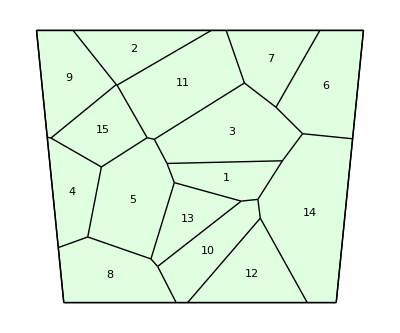

```mathematica
ShowTissue[w, "CellNumbers"-> True]
```

```mathematica
T=MergeCells[w,{1,3}]
```

Tissue[{{-0.470307,6.04561},{0.879713,2.41112},{1.38019,4.9823},{1.9271,8.0101},{1.95613,7.98974},{3.05994,6.05757},{3.19961,1.60412},{3.32274,5.99916},{3.44551,1.32781},{3.78981,5.11191},{4.05743,4.4067},{6.51287,3.72766},{6.63058,8.06882},{7.12445,3.79228},{7.2137,3.10115},{7.78871,7.17731},{8.02584,5.20993},{8.76649,6.20449},{11,10},{-1,10},{0,0},{10,0},{9.39927,10.},{5.96133,10.},{5.41435,10.},{0.341094,10.},{-0.607511,6.07511},{-0.20198,2.0198},{4.1252,0.},{4.54534,0.},{8.93618,0.},{10.6019,6.01862}},{{1,3},{1,4},{1,27},{2,3},{2,7},{2,28},{3,6},{4,5},{4,26},{5,6},{5,25},{6,8},{7,9},{7,11},{8,10},{8,13},{9,12},{9,29},{10,11},{10,17},{11,12},{12,14},{13,16},{13,24},{14,15},{14,17},{15,30},{15,31},{16,18},{16,23},{17,18},{18,32},{19,23},{19,32},{20,26},{20,27},{21,28},{21,29},{22,31},{22,32},{23,24},{24,25},{25,26},{27,28},{29,30},{30,31}},{{43,9,8,11},{44,6,4,1,3},{4,5,14,19,15,12,7},{30,29,32,34,33},{41,24,23,30},{38,18,13,5,6,37},{36,3,2,9,35},{45,27,25,22,17,18},{42,11,10,12,16,24},{46,28,27},{13,17,21,14},{40,32,31,26,25,28,39},{1,7,10,8,2},{15,19,21,22,26,31,29,23,16}}]

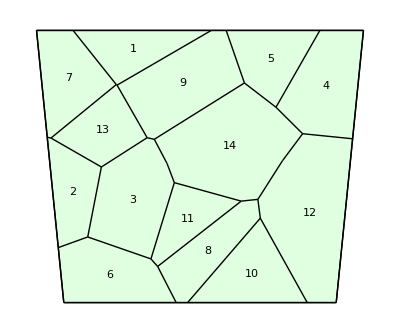

```mathematica
ShowTissue[T, "CellNumbers"-> True]
```